```mathematica
German Credit Data

trainyes=Import[FileNameJoin[{NotebookDirectory[],"german_numeric_train_yes.txt"}],"Table"]; (* Using relative path for porting situation *)trainno=Import[FileNameJoin[{NotebookDirectory[],"german_numeric_train_no.txt"}],"Table"];
testyes=Import[FileNameJoin[{NotebookDirectory[],"german_numeric_test_yes.txt"}],"Table"];
testno=Import[FileNameJoin[{NotebookDirectory[],"german_numeric_test_no.txt"}],"Table"];
ruleyes=Rule[#,1]&/@trainyes; (* Creating rules to feed Classify *)
ruleno=Rule[#,2]&/@trainno;
testyes=Rule[#,1]&/@testyes;
testno=Rule[#,2]&/@testno;
cl3=Classify[Join[ruleyes,ruleno],Method->"SupportVectorMachine",FeatureTypes->Automatic]; (* Train Classify *)
ClassifierInformation[cl3] (* Get basic information *)
```

Credit Data German

Classifier information
Method | Support vector machine
Number of classes | 2
Number of features | 24
Number of training examples | 900
Number of extracted features | 44
Kernel type | Radial basis function
Soft margin parameter | 16384.

```mathematica
cm = ClassifierMeasurements[cl3, Join[testyes,testno]]
```

ClassifierMeasurementsObject[…]

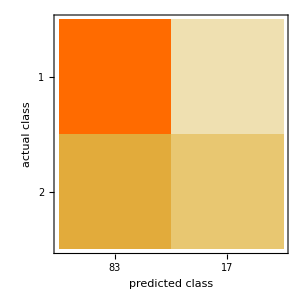

```mathematica
cm["ConfusionMatrixPlot"]
```

```mathematica
cm["Accuracy"]
```

0.79

```mathematica
cm["AreaUnderROCCurve"]
```

<|1→0.825714,2→0.825714|>

```mathematica
cm["ClassRejectionRate"]
```

<|1→0.,2→0.|>

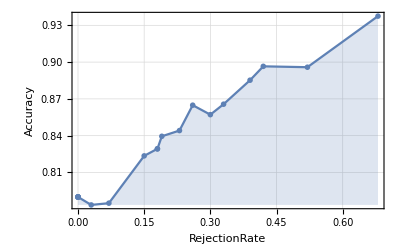

```mathematica
cm["AccuracyRejectionPlot"]
```

```mathematica
cm["DecisionUtilities"]
```

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.,1.,1.,1.,1.,0.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.,0.,1.,1.,0.,1.,1.,0.,1.,0.,1.,0.,0.,1.,1.,0.,1.,0.,1.,1.,0.,0.,0.,1.,0.,0.,0.,0.,0.}

```mathematica
cm["GeometricMeanProbability"]
```

0.592158

```mathematica
cm["LogLikelihood"]
```

-52.3981

```mathematica
cm["MisclassifiedExamples"]
```

{{4,36,0,26,1,3,3,2,3,27,3,2,1,1,1,0,0,1,0,0,1,0,0,1}→1,{1,24,2,24,1,5,3,4,1,64,1,1,1,1,1,0,0,1,0,1,0,0,1,0}→1,{2,48,1,122,5,1,3,4,4,36,3,1,1,2,1,1,0,0,1,0,0,0,0,0}→1,{1,15,2,14,1,3,2,4,3,28,3,1,1,1,1,1,0,1,0,1,0,0,0,1}→1,{2,24,4,47,1,2,2,4,3,25,1,1,1,1,1,0,0,1,0,0,1,0,1,0}→2,{3,18,2,21,1,3,3,2,1,37,2,1,1,1,1,0,0,0,1,0,1,0,0,1}→2,{2,18,2,130,1,1,2,4,4,38,3,1,1,2,1,0,1,1,0,0,0,0,0,0}→2,{2,15,2,8,1,5,3,3,3,37,3,1,2,1,1,0,0,1,0,0,1,0,0,1}→2,{2,9,2,17,1,2,2,2,3,22,3,1,1,2,1,0,0,1,0,0,1,0,0,1}→2,{4,48,2,39,5,3,1,2,1,38,1,1,1,1,1,0,0,1,0,0,1,0,0,1}→2,{2,36,2,27,2,3,2,4,4,50,3,1,1,1,1,0,0,0,1,0,0,0,0,1}→2,{4,18,3,22,1,3,4,2,3,28,3,1,1,2,1,0,0,1,0,0,1,0,0,1}→2,{1,12,4,48,1,5,3,4,2,43,3,2,1,2,1,1,0,0,1,1,0,0,0,1}→2,{1,6,1,12,1,5,2,4,4,35,3,1,1,1,1,0,0,1,0,0,0,0,0,1}→2,{2,30,4,84,1,4,3,2,2,49,3,1,1,1,1,0,0,1,0,0,1,0,0,1}→2,{4,36,4,79,1,3,2,2,1,25,2,2,1,2,1,1,0,1,0,0,1,0,0,1}→2,{2,12,2,15,5,3,4,1,1,25,3,1,1,2,1,0,0,1,0,0,1,0,0,1}→2,{1,24,3,10,1,2,4,4,1,48,2,1,1,1,1,0,0,1,0,0,1,0,0,1}→2,{1,18,2,75,5,5,3,4,2,51,3,1,2,2,1,0,1,1,0,0,0,0,0,1}→2,{1,12,4,22,1,5,3,3,2,60,3,2,1,1,1,0,0,1,0,0,1,0,0,1}→2,{4,18,4,15,1,3,3,2,2,32,1,2,1,1,1,1,0,1,0,0,1,0,0,1}→2}

```mathematica
cm["Precision"]
```

<|1→0.795181,2→0.764706|>

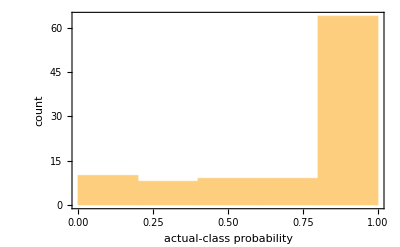

```mathematica
cm["ProbabilityHistogram"]
```

```mathematica
cm["Properties"]
```

{Accuracy,AccuracyRejectionPlot,AreaUnderROCCurve,BestClassifiedExamples,ClassifierFunction,ClassMeanCrossEntropy,ClassRejectionRate,CohenKappa,ConfusionFunction,ConfusionMatrix,ConfusionMatrixPlot,CorrectlyClassifiedExamples,DecisionUtilities,Error,Examples,F1Score,FalseDiscoveryRate,FalseNegativeExamples,FalseNegativeRate,FalsePositiveExamples,FalsePositiveRate,GeometricMeanProbability,IndeterminateExamples,LeastCertainExamples,Likelihood,LogLikelihood,MatthewsCorrelationCoefficient,MeanCrossEntropy,MeanDecisionUtility,MisclassifiedExamples,MostCertainExamples,NegativePredictedValue,Perplexity,Precision,Probabilities,ProbabilityHistogram,Properties,Recall,RejectionRate,ROCCurve,ScottPi,Specificity,TopConfusions,TrueNegativeExamples,TruePositiveExamples,WorstClassifiedExamples}

```mathematica
cm["ScottPi"]
```

0.415937

```mathematica
cm["Specificity"]
```

<|1→0.433333,2→0.942857|>

```mathematica
cm["TopConfusions"]
```

{1→2}

```mathematica
cm["WorstClassifiedExamples"]
```

{{2,12,2,15,5,3,4,1,1,25,3,1,1,2,1,0,0,1,0,0,1,0,0,1}→2,{4,18,3,22,1,3,4,2,3,28,3,1,1,2,1,0,0,1,0,0,1,0,0,1}→2,{1,18,2,75,5,5,3,4,2,51,3,1,2,2,1,0,1,1,0,0,0,0,0,1}→2,{1,12,4,22,1,5,3,3,2,60,3,2,1,1,1,0,0,1,0,0,1,0,0,1}→2,{3,18,2,21,1,3,3,2,1,37,2,1,1,1,1,0,0,0,1,0,1,0,0,1}→2,{2,30,4,84,1,4,3,2,2,49,3,1,1,1,1,0,0,1,0,0,1,0,0,1}→2,{2,15,2,8,1,5,3,3,3,37,3,1,2,1,1,0,0,1,0,0,1,0,0,1}→2,{4,48,2,39,5,3,1,2,1,38,1,1,1,1,1,0,0,1,0,0,1,0,0,1}→2,{1,15,2,14,1,3,2,4,3,28,3,1,1,1,1,1,0,1,0,1,0,0,0,1}→1,{4,18,4,15,1,3,3,2,2,32,1,2,1,1,1,1,0,1,0,0,1,0,0,1}→2}

```mathematica
ClassifierInformation[cl3, "Properties"]
```

{BiasParameter,Classes,ClassNumber,ClassPriors,ExampleNumber,ExtractedFeatureNumber,FeatureNames,FeatureNumber,FeatureTypes,FunctionProperties,GammaScalingParameter,HyperparameterOptimizationMethod,IndeterminateThreshold,KernelType,MaxTrainingMemory,Method,MethodDescription,MulticlassMethod,PerformanceGoal,PolynomialDegree,Properties,SoftMarginParameter,SupportVectorNumbers,TrainingClassPriors,TrainingTime,UtilityFunction}

```mathematica
Australian Credit Data

autrainyes=Import[FileNameJoin[{NotebookDirectory[],"australian_train_yes.txt"}],"Table"];
autrainno=Import[FileNameJoin[{NotebookDirectory[],"australian_train_no.txt"}],"Table"];
autestyes=Import[FileNameJoin[{NotebookDirectory[],"australian_test_yes.txt"}],"Table"];
autestno=Import[FileNameJoin[{NotebookDirectory[],"australian_test_no.txt"}],"Table"];
auruleyes=Rule[#,1]&/@autrainyes;
auruleno=Rule[#,2]&/@autrainno;
autestyes=Rule[#,1]&/@autestyes;
autestno=Rule[#,2]&/@autestno;
aucl=Classify[Join[auruleyes,auruleno],Method->"SupportVectorMachine",FeatureTypes->Automatic];
ClassifierInformation[aucl]
```

Australian Credit Data

Classifier information
Method | Support vector machine
Number of classes | 2
Number of features | 14
Number of training examples | 622
Number of extracted features | 18
Kernel type | Radial basis function
Soft margin parameter | 2.82843

```mathematica
aucm = ClassifierMeasurements[aucl, Join[autestyes,autestno]]
```

ClassifierMeasurementsObject[…]

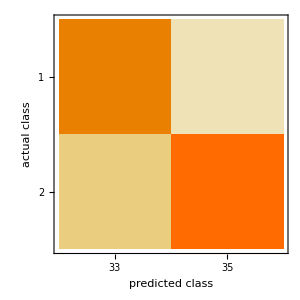

```mathematica
aucm["ConfusionMatrixPlot"]
```

```mathematica
aucm["Accuracy"]
```

0.926471

```mathematica
aucm["AreaUnderROCCurve"]
```

<|1→0.992105,2→0.992105|>

```mathematica
aucm["ClassRejectionRate"]
```

<|1→0.,2→0.|>

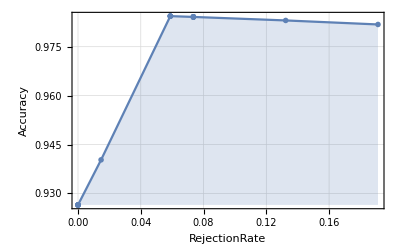

```mathematica
aucm["AccuracyRejectionPlot"]
```

```mathematica
aucm["DecisionUtilities"]
```

{1.,1.,1.,1.,1.,1.,1.,0.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.,1.,1.,1.,1.,1.,1.,1.,0.,1.,1.,1.,1.,1.,1.,0.}

```mathematica
aucm["GeometricMeanProbability"]
```

0.88818

```mathematica
aucm["LogLikelihood"]
```

-8.06346

```mathematica
aucm["MisclassifiedExamples"]
```

{{0,22.5,8.46,1,14,4,2.46,0,0,0,0,2,164,1}→1,{1,16.25,0.835,2,7,4,0.085,1,0,0,0,1,200,1}→2,{1,42.75,3,2,3,5,1,1,0,0,0,2,0,201}→2,{1,39.83,0.5,2,7,4,0.25,1,0,0,0,1,288,1}→2,{1,25.67,2.21,1,6,4,4,1,0,0,0,2,188,1}→2}

```mathematica
aucm["Precision"]
```

<|1→0.878788,2→0.971429|>

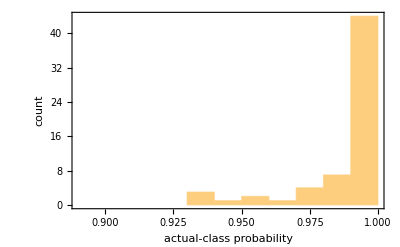

```mathematica
aucm["ProbabilityHistogram"]
```

```mathematica
aucm["Properties"]
```

{Accuracy,AccuracyRejectionPlot,AreaUnderROCCurve,BestClassifiedExamples,ClassifierFunction,ClassMeanCrossEntropy,ClassRejectionRate,CohenKappa,ConfusionFunction,ConfusionMatrix,ConfusionMatrixPlot,CorrectlyClassifiedExamples,DecisionUtilities,Error,Examples,F1Score,FalseDiscoveryRate,FalseNegativeExamples,FalseNegativeRate,FalsePositiveExamples,FalsePositiveRate,GeometricMeanProbability,IndeterminateExamples,LeastCertainExamples,Likelihood,LogLikelihood,MatthewsCorrelationCoefficient,MeanCrossEntropy,MeanDecisionUtility,MisclassifiedExamples,MostCertainExamples,NegativePredictedValue,Perplexity,Precision,Probabilities,ProbabilityHistogram,Properties,Recall,RejectionRate,ROCCurve,ScottPi,Specificity,TopConfusions,TrueNegativeExamples,TruePositiveExamples,WorstClassifiedExamples}

```mathematica
aucm["ScottPi"]
```

0.852142

```mathematica
aucm["Specificity"]
```

<|1→0.894737,2→0.966667|>

```mathematica
aucm["TopConfusions"]
```

{1→2}

```mathematica
aucm["WorstClassifiedExamples"]
```

{{0,22.5,8.46,1,14,4,2.46,0,0,0,0,2,164,1}→1,{1,39.83,0.5,2,7,4,0.25,1,0,0,0,1,288,1}→2,{1,25.67,2.21,1,6,4,4,1,0,0,0,2,188,1}→2,{1,42.75,3,2,3,5,1,1,0,0,0,2,0,201}→2,{1,16.25,0.835,2,7,4,0.085,1,0,0,0,1,200,1}→2,{1,20.5,10,1,8,4,2.5,1,0,0,0,1,40,1}→1,{1,18.5,2,2,3,4,1.5,1,1,2,0,2,120,301}→1,{0,18.25,10,2,9,4,1,0,1,1,0,2,120,2}→2,{1,47.83,4.165,2,14,5,0.085,0,0,0,1,2,520,1}→2,{0,32.33,0.54,2,13,4,0.04,1,0,0,0,2,440,11178}→1}

```mathematica
ClassifierInformation[aucl, "Properties"]
```

{BiasParameter,Classes,ClassNumber,ClassPriors,ExampleNumber,ExtractedFeatureNumber,FeatureNames,FeatureNumber,FeatureTypes,FunctionProperties,GammaScalingParameter,HyperparameterOptimizationMethod,IndeterminateThreshold,KernelType,MaxTrainingMemory,Method,MethodDescription,MulticlassMethod,PerformanceGoal,PolynomialDegree,Properties,SoftMarginParameter,SupportVectorNumbers,TrainingClassPriors,TrainingTime,UtilityFunction}

```mathematica
aucl2=Classify[Join[auruleyes,auruleno],Method->{"SupportVectorMachine", "KernelType"->"RadialBasisFunction"},FeatureTypes->Automatic];
ClassifierInformation[aucl2]
aucm2 = ClassifierMeasurements[aucl2, Join[autestyes,autestno]]
```

Classifier information
Method | Support vector machine
Number of classes | 2
Number of features | 14
Number of training examples | 622
Number of extracted features | 18
Kernel type | Radial basis function
Soft margin parameter | 0.0947323

ClassifierMeasurementsObject[…]

```mathematica
gecl=Classify[Join[ruleyes,ruleno],Method->{"SupportVectorMachine", "KernelType"->"RadialBasisFunction"},FeatureTypes->Automatic]; (* Train Classify *)
ClassifierInformation[gecl] 
gecm = ClassifierMeasurements[gecl, Join[testyes,testno]]
```

Classifier information
Method | Support vector machine
Number of classes | 2
Number of features | 24
Number of training examples | 900
Number of extracted features | 44
Kernel type | Radial basis function
Soft margin parameter | 8.

ClassifierMeasurementsObject[…]

```mathematica
References:
```

```mathematica
- functionalities
https://mathematica.stackexchange.com/questions/14987/machine-learning-svm-algorithm 
https://www.reddit.com/r/Mathematica/comments/2rzjd3/classify_and_kernel_svm_in_mathematica/
https://mathematica.stackexchange.com/questions/6013/relative-paths-for-portable-notebooks-in-mathematica

 - possible bugs in Mathematica
https://mathematica.stackexchange.com/questions/106008/how-to-get-the-training-error-and-the-validation-error-using-classify-function-w
https://mathematica.stackexchange.com/questions/106195/error-when-training-support-vector-machine-svm-classifier
```